# Leading order cross section for qq̄→(χ̃)_i^±(χ̃)_j^∓

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of three packages found in the “include” folder.

```mathematica
description = "Leading order cross section of chargino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< TreeLevel`
<< CalcTools`
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

## Generate Feynman diagrams and amplitudes

Some text

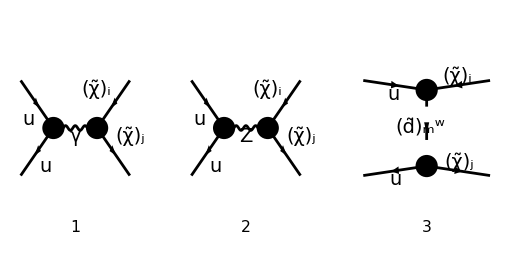

```mathematica
treeDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 2, ExcludeTopologies -> {Boxes,SelfEnergies,Tadpoles}], 
	{F[3, {1, a}], -F[3, {1, b}]} -> {-F[12, {i}], F[12, {j}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling,NoElectronHCoupling},
	ExcludeParticles -> {F[11],F[12],S[1],S[2],S[3],S[4]}
];
Paint[treeDiagrams, Numbering->Simple, ColumnsXRows -> {3, 1}, ImageSize->{512,256}];
```

```mathematica
M0[0] = FCFAConvert[
	CreateFeynAmp[treeDiagrams], 
	IncomingMomenta -> {ki,kj},
	OutgoingMomenta -> {pi,pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> True,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
]/.{IndexDelta -> FeynCalc`IndexDelta};
```

```mathematica
tempPrefactor = SMP["g_W"]^2 FeynCalc`IndexDelta[a,b];
M0[1] = tempPrefactor*DiracSimplify /@ (Convert2QZCharges /@ (M0[0]/tempPrefactor));
M0[2] = M0[1] //. SuperChargeRules;
Clear[tempPrefactor]
```

```mathematica
MA[0] = Part[M0[0], 1] //. ASimplifyRules /. FeynCalc`IndexDelta[a,b] -> 3/2 Qe FeynCalc`IndexDelta[a,b] // Simplify;
MZ[0] = Part[M0[0], 2] /. ASimplifyRules /. {Op[j,i,x_] -> Op[i,j,x]*, FeynCalc`IndexDelta[j,i] -> FeynCalc`IndexDelta[i,j]} /. ZSimplifyRules // Simplify;
MQ[0] = Part[M0[0], 3] //. QSimplifyRules // Simplify;
```

Divide the three amplitudes into separate channels and convert to Q_A^XY and Z_s^X supercharges.

```mathematica
MA[1] = MA[0] // FeynAmpDenominatorExplicit
MZ[1] = (MZ[0] // FeynAmpDenominatorExplicit) /. SMP["m_Z"]^2->DZ
MQ[1] = (MQ[0] // FeynAmpDenominatorExplicit) /. Index[Sfermion,5]->A

MAC[1] = ConjugateAmplitude[MA[1]]/.{A->B,μ->ρ,ν->σ};
MZC[1] = ConjugateAmplitude[MZ[1]]/.{A->B,μ->ρ,ν->σ};
MQC[1] = ConjugateAmplitude[MQ[1]]/.{A->B,μ->ρ,ν->σ};
```

-(g^μν (φ(-k_j)).(-ⅈ Qe γ^μ g_W δ_ab (sin(θ_W))).(φ(k_i)) (φ(p_j,m_j)).(ⅈ γ^ν g_W δ_ij (sin(θ_W))).(φ(-p_i,m_i)))/s

-(g^μν (φ(-k_j)).(-ⅈ g_W δ_ab (γ^μ.(γ̄)^7 C_qqZ^L+γ^μ.(γ̄)^6 C_qqZ^R)).(φ(k_i)) (φ(p_j,m_j)).(-ⅈ g_W (γ^ν.(γ̄)^6 O_ij^(′L)+γ^ν.(γ̄)^7 O_ij^(′R))).(φ(-p_i,m_i)))/(s-Δ_Z)

-((φ(-k_i)).(-2 ⅈ (γ̄)^7 g_W Conjugate[(C_(q'(q̃)_A(χ̃)_i^±)^L)]).(φ(-p_i,m_i)) (φ(-k_j)).(-2 ⅈ (γ̄)^6 g_W δ_ab C_(q'(q̃)_A(χ̃)_j^±)^L).(φ(-p_j,m_j)))/(t-m_((d̃)_(Gen5,A))^2)

Save results in “results/LO/amps.m”
They can be loaded with
LOAmps=Import[FileNameJoin[{ResultsDir,"amps.m"}]];
which creates a list containing the s, t, u amplitudes followed by their conjugates in the same order.

```mathematica
(*Export[FileNameJoin[{ResultsDir, "amps.m"}], ToString/@FullForm/@{Ms[0],Mt[0],Mu[0],MsC[0],MtC[0],MuC[0]}];*)
```

## Differential Cross-Section

Some more text

```mathematica
IAA[0] = SquareAmplitudes[MA[1],MAC[1]];
IZZ[0] = SquareAmplitudes[MZ[1],MZC[1]];
IQQ[0] = SquareAmplitudes[MQ[1],MQC[1]];
IAZ[0] = (SquareAmplitudes[MA[1],MZC[1]]+SquareAmplitudes[MZ[1],MAC[1]])/2;
IAQ[0] = (SquareAmplitudes[MA[1],MQC[1]/.B->A]+SquareAmplitudes[MQ[1],MAC[1]])/2;
IZQ[0] = (SquareAmplitudes[MZ[1],MQC[1]/.B->A]+SquareAmplitudes[MQ[1],MZC[1]])/2;
```

Convert the dimension D→4.

```mathematica
IAA[1] = FixDimension[IAA[0]/.Convert2Den];
IZZ[1] = FixDimension[IZZ[0]/.Convert2Den];
IQQ[1] = FixDimension[IQQ[0]/.Convert2Den];
IAZ[1] = FixDimension[IAZ[0]/.Convert2Den];
IAQ[1] = FixDimension[IAQ[0]/.Convert2Den];
IZQ[1] = FixDimension[IZQ[0]/.Convert2Den];
```

Draw out common prefactor between the squared amplitudes and factor them in terms of denominators and basic kinematic terms.

```mathematica
CommonPrefactor = 4 (FeynCalc`IndexDelta[a,b])^2 SMP["g_W"]^4;
IAA[2] = CommonPrefactor FactorDenominators[IAA[1]/CommonPrefactor];
IZZ[2] = CommonPrefactor FactorDenominators[IZZ[1]/CommonPrefactor];
IQQ[2] = CommonPrefactor FactorDenominators[IQQ[1]/CommonPrefactor];
IAZ[2] = CommonPrefactor FactorDenominators[IAZ[1]/CommonPrefactor];
IAQ[2] = CommonPrefactor FactorDenominators[IAQ[1]/CommonPrefactor];
IZQ[2] = CommonPrefactor FactorDenominators[IZQ[1]/CommonPrefactor];
```

We can convert these to  Q_A^XY and Z_s^X supercharges, and write them out in a nice form using this.

```mathematica
CommonPrefactor Collect[
	IZQ[2]/CommonPrefactor //. SuperChargeRules // TrickMandelstam[#, MandelstamParameters]&,
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	Factor2
]
```

4 g_W^4 δ_ab^2 (-1/s 1/(t-m_((d̃)_(Gen5,A))^2) (-s t m_i^2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-s t m_j^2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+s m_i^2 m_j^2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+s^2 m_i m_j Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)]+s t^2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-s t m_i^2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR-s t m_j^2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR+s m_i^2 m_j^2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR+s^2 m_i m_j Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL+s t^2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR-Qe t m_i^2 δ_ij (sin(θ_W))^2 Conjugate[(Q_A^LL)]-Qe t m_j^2 δ_ij (sin(θ_W))^2 Conjugate[(Q_A^LL)]+Qe m_i^2 m_j^2 δ_ij (sin(θ_W))^2 Conjugate[(Q_A^LL)]+Qe t^2 δ_ij (sin(θ_W))^2 Conjugate[(Q_A^LL)]-Qe t m_i^2 Q_A^LL δ_ij (sin(θ_W))^2-Qe t m_j^2 Q_A^LL δ_ij (sin(θ_W))^2+Qe m_i^2 m_j^2 Q_A^LL δ_ij (sin(θ_W))^2+Qe t^2 Q_A^LL δ_ij (sin(θ_W))^2)-Qe m_i m_j δ_ij (sin(θ_W))^2 (Conjugate[(Q_A^LL)]+Q_A^LL) 1/(t-m_((d̃)_(Gen5,A))^2))

Add all squared amplitudes, omitting the common prefactor.

```mathematica
Itot[0] = (IAA[2]+IZZ[2]+IQQ[2]+2IAZ[2]+2IAQ[2]+2IZQ[2])/CommonPrefactor;
Itot[1] = Collect[
	Itot[0],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(Collect[
		#1,
		Den[args1__]Den[args2__],
		(Simplify[Expand[#1]//.SuperChargeRules]&)
	]&)
];
Itot[0] //
	ReplaceAll[#, Qe -> s Den[s, 0] Qe]& //
	Expand //
	ReplaceRepeated[#, {s*t -> MEW[i]^2*t+MEW[j]^2*t-t^2-u*t, s*u -> MEW[i]^2*u+MEW[j]^2*u-t*u-u^2}]& //
	Expand //
	ReplaceRepeated[#, {t^2 -> ti tj+t(MEW[i]^2+MEW[j]^2)-MEW[i]^2MEW[j]^2, u^2 -> ui uj+u(MEW[i]^2+MEW[j]^2)-MEW[i]^2MEW[j]^2}]& //
	ReplaceRepeated[#, SuperChargeRules]& //
	ReplaceAll[#, {ti -> titj/tj, ui -> uiuj/uj, MEW[i]MEW[j] -> MEW[ij]}]& //
	Expand //
	Collect2[#, {titj, uiuj, MEW[ij]}, Factoring -> Isolate]&
	(*Collect2[
		#,
		{MEW[i]*MEW[j], ti tj, ui uj, t*u-MEW[i]^2*MEW[j]^2},
		Factoring -> Isolate
	]&*) (*// FRH // ReplaceAll[#, {ti -> t-MEW[i]^2, tj -> t-MEW[j]^2, ui -> u-MEW[j]^2, uj -> u-MEW[j]^2}]&*)
```

KK(1267) m_ij+KK(1263) titj+KK(1265) uiuj+KK(1261)

Show that the total amplitude can be written as effective charges in front of four different kinematic terms.

```mathematica
Collect[
	Itot[1],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(Isolate[#1//Simplify,IsolateNames->Q]&)
]
```

Q(1271) s m_i m_j+Q(1276) (t-m_i^2) (t-m_j^2)+Q(1278) (u-m_i^2) (u-m_j^2)-Q(1284)

```mathematica
Itot[1] /.
	{Zij["CC"][L,L] -> Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][L,R] -> Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,R] -> Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,L] -> Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s} //
	TrickMandelstam[#, MandelstamParameters]& //
	ReplaceRepeated[#, {Conjugate[a_+b_] -> a*b*, Conjugate[a_*b_] -> a*b*}]& //
	Refine[#, Assumptions->{Qe ∈ Reals, s ∈ PositiveReals, FeynCalc`IndexDelta[__] ∈ Integers, SMP[_] ∈ Reals}]& //
	Expand //
	ReplaceRepeated[#, {s*t -> MEW[i]^2*t+MEW[j]^2*t-t^2-u*t, s*u -> MEW[i]^2*u+MEW[j]^2*u-t*u-u^2}]& //
	Expand //
	ReplaceRepeated[#, {t^2 -> ti tj+t(MEW[i]^2+MEW[j]^2)-MEW[i]^2MEW[j]^2, u^2 -> ui uj+u(MEW[i]^2+MEW[j]^2)-MEW[i]^2MEW[j]^2}]& //
	Expand //
	TrickMandelstam[#, MandelstamParameters]&;

Collect[
	%,
	{MEW[i]*MEW[j], ti tj, ui uj, t*u-MEW[i]^2*MEW[j]^2},
	(Isolate[#1//Simplify,IsolateNames->Q]&)
]
```

Q(1318) m_i m_j+Q(1321) ti tj+Q(1325) ui uj

```mathematica
(*IAA[2] + IZZ[2] + 2IAZ[2]*)
(*2IAQ[2] + 2IZQ[2]*)
Itot[0] //
	Expand //
	ReplaceRepeated[#, SuperChargeRules]& //
(*	ReplaceAll[#, {Zij["CC"][L,L] -> Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][L,R] -> Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,R] -> Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,L] -> Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s}]& //*)
	TrickMandelstam[#, MandelstamParameters]& //
	ReplaceRepeated[#, {Conjugate[a_+b_] -> a*b*, Conjugate[a_*b_] -> a*b*}]& //
	Refine[#, Assumptions->{Qe ∈ Reals, s ∈ PositiveReals, FeynCalc`IndexDelta[__] ∈ Integers, SMP[_] ∈ Reals}]& //
	Expand //
	ReplaceRepeated[#, {s*t -> MEW[i]^2*t+MEW[j]^2*t-t^2-u*t, s*u -> MEW[i]^2*u+MEW[j]^2*u-t*u-u^2}]& //
	Expand //
	ReplaceRepeated[#, {t^2 -> ti tj+t(MEW[i]^2+MEW[j]^2)-MEW[i]^2MEW[j]^2, u^2 -> ui uj+u(MEW[i]^2+MEW[j]^2)-MEW[i]^2MEW[j]^2}]& //
	Expand //
	TrickMandelstam[#, MandelstamParameters]&;

Collect[
	%,
	{MEW[i]*MEW[j], ti tj, ui uj, t*u-MEW[i]^2*MEW[j]^2},
	(Isolate[#1//Simplify,IsolateNames->Q]&)
]


% /. {ti -> t-MEW[i]^2, tj -> t - MEW[j]^2, ui -> u-MEW[i]^2, uj -> u-MEW[j]^2} //
	FRH //
	(*ReplaceAll[
		#,
		{Zij["CC"][L,L] -> Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
			Zij["CC"][L,R] -> Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
			Zij["CC"][R,R] -> Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
			Zij["CC"][R,L] -> Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s}
	]& //*)
	Refine[#, Assumptions->{Qe ∈ Reals, s ∈ PositiveReals, FeynCalc`IndexDelta[__] ∈ Integers, SMP[_] ∈ Reals}]& //
	Expand // 
	TrickMandelstam[#, MandelstamParameters]& // FullSimplify
	
Itot[1] = % // Collect2[#, {(Qst|Qsu)[_], Qtu[__]}, Factoring -> FullSimplify]& //
	Collect[#, {(t-MEW[i]^2)(t-MEW[j]^2), (u-MEW[i]^2)(u-MEW[j]^2), s MEW[i]MEW[j]}, FullSimplify]&
```

Q(1353) m_i m_j+Q(1355) ti tj+Q(1356) ui uj

-2 Conjugate[(Q_A^LL)] 1/(t-m_((d̃)_(Gen5,A))^2) ((t-m_i^2) (t-m_j^2) Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+s m_i m_j Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)]+2 Q_B^LL (m_i^2-t) (t-m_j^2) 1/(t-m_((d̃)_(Gen5,B))^2))-2 t^2 Q_A^LL 1/(t-m_((d̃)_(Gen5,A))^2) Z_((χ̃)_i^±(χ̃)_j^∓)^LR+2 t m_i^2 Q_A^LL 1/(t-m_((d̃)_(Gen5,A))^2) Z_((χ̃)_i^±(χ̃)_j^∓)^LR+2 t m_j^2 Q_A^LL 1/(t-m_((d̃)_(Gen5,A))^2) Z_((χ̃)_i^±(χ̃)_j^∓)^LR-2 m_i^2 m_j^2 Q_A^LL 1/(t-m_((d̃)_(Gen5,A))^2) Z_((χ̃)_i^±(χ̃)_j^∓)^LR-2 s m_i m_j Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL 1/(t-m_((d̃)_(Gen5,A))^2)+(t-m_i^2) (t-m_j^2) Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+(t-m_i^2) (t-m_j^2) Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2+(u-m_i^2) (u-m_j^2) Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2-u m_i^2 Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2-u m_j^2 Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2+m_i^2 m_j^2 Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2+u^2 Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2+s m_i m_j Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+s m_i m_j Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)] Z_((χ̃)_i^±(χ̃)_j^∓)^LR+s m_i m_j Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL+s m_i m_j Z_((χ̃)_i^±(χ̃)_j^∓)^RR Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RL)]

(t-m_i^2) (t-m_j^2) (-2 1/(t-m_((d̃)_(Gen5,A))^2) (Conjugate[(Q_A^LL)] (Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-2 Q_B^LL 1/(t-m_((d̃)_(Gen5,B))^2))+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR)+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2)+s m_i m_j (-2 1/(t-m_((d̃)_(Gen5,A))^2) (Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)]+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL)+Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)] Z_((χ̃)_i^±(χ̃)_j^∓)^LR+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL+Z_((χ̃)_i^±(χ̃)_j^∓)^RR Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RL)])+(u-m_i^2) (u-m_j^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)

```mathematica
FRH[-Q[2049](t-MEW[i]^2)(t-MEW[j]^2) + Q[2050](u-MEW[i]^2)(u-MEW[j]^2) - 2Q[1931]] /. 
	{Zij["CC"][L,L] -> Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][L,R] -> Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,R] -> Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,L] -> Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s} //
	Refine[#, Assumptions->{Qe ∈ Reals, s ∈ PositiveReals, FeynCalc`IndexDelta[__] ∈ Integers, SMP[_] ∈ Reals}]& //
	Expand // 
	TrickMandelstam[#, MandelstamParameters]& // FullSimplify
```

Q(2050) (u-m_i^2) (u-m_j^2)-Q(2049) m_i^2 m_j^2+Q(2049) t m_i^2+Q(2049) t m_j^2-Q(2049) t^2-2 Q(1931)

```mathematica
FRH[-Q[2107]MEW[i]MEW[j] - Q[2110](t-MEW[i]^2)(t-MEW[j]^2)] /. 
	{Zij["CC"][L,L] -> Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][L,R] -> Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,R] -> Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,L] -> Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s} //
	Refine[#, Assumptions->{Qe ∈ Reals, s ∈ PositiveReals, FeynCalc`IndexDelta[__] ∈ Integers, SMP[_] ∈ Reals}]& //
	Expand // 
	TrickMandelstam[#, MandelstamParameters]& // FullSimplify
```

Q(2110) (m_i^2-t) (t-m_j^2)-Q(2107) m_i m_j

```mathematica
FRH[Q[1588]MEW[i]MEW[j] + Q[1591](t-MEW[i]^2)(t-MEW[j]^2) + Q[1597](u-MEW[i]^2)(u-MEW[j]^2) + 2Q[1325]] /. 
	{Zij["CC"][L,L] -> Qsu[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][L,R] -> Qst[L] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,R] -> Qsu[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s,
	Zij["CC"][R,L] -> Qst[R] + (Qe SMP["sin_W"]^2 FeynCalc`IndexDelta[i,j])/s} //
	Refine[#, Assumptions->{Qe ∈ Reals, s ∈ PositiveReals, FeynCalc`IndexDelta[__] ∈ Integers, SMP[_] ∈ Reals}]& //
	Expand // 
	TrickMandelstam[#, MandelstamParameters]& // FullSimplify
```

(2 Qe δ_ij (sin(θ_W))^2 (Abs[Qsu(L)]^2+Abs[Qsu(R)]^2))/s+(2 Qe^2 δ_ij^2 (sin(θ_W))^4 (Conjugate[Qsu(L)]+Conjugate[Qsu(R)]))/s^2+m_i^2 (Q(1591) (m_j^2-t)+Q(1597) (m_j^2-u))+Q(1588) m_i m_j+Q(1591) t (t-m_j^2)+Q(1597) u (u-m_j^2)

Calculate the total differential cross section and save to “results/LO/dxsec.m”

```mathematica
DiffXSecPrefactor = CommonPrefactor/(64 Pi CA^2 s^2)IdenticalPartFactor[i,j] /. {(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]};
DiffXSec = DiffXSecPrefactor Itot[1] /. {(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]}

(*Export[FileNameJoin[{ResultsDir, "dxsec.m"}], FullForm[DiffXSec]//ToString];*)
```

1/(s^2 C_A)π α_W^2 (1/2)^(i,j) ((t-m_i^2) (t-m_j^2) (-2 1/(t-m_((d̃)_(Gen5,A))^2) (Conjugate[(Q_A^LL)] (Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-2 Q_B^LL 1/(t-m_((d̃)_(Gen5,B))^2))+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR)+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2)+s m_i m_j (-2 1/(t-m_((d̃)_(Gen5,A))^2) (Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)]+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL)+Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)] Z_((χ̃)_i^±(χ̃)_j^∓)^LR+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL+Z_((χ̃)_i^±(χ̃)_j^∓)^RR Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RL)])+(u-m_i^2) (u-m_j^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2))

```mathematica
DiffXSecPrefactor Collect[
	ReplaceAll[DiffXSec/DiffXSecPrefactor, {DSf[args__]->MSf[args]^2, DZ->SMP["m_Z"]^2, DSfC[args__]->MSf[args]^2}],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(Collect[
		#1,
		Den[args1__]Den[args2__],
		(FullSimplify[Expand[#1]/.{Opp[args__,L]*->-Opp[args,R],Opp[args__,R]*->-Opp[args,L]}//.SuperChargeRules]&)
	]&)
] // Refine[#, Assumptions->{SMP[_]∈Reals, MSf[__]∈Reals}]&;
% //. {a_+a_* -> 2Re[a], a_ b_+a_*b_* -> 2Re[a b], a_ b_*+a_*b_ -> 2Re[a b*], a_^2+a_*^2 -> 2Re[a^2]}
```

1/(s^2 C_A)π α_W^2 (1/2)^(i,j) ((t-m_i^2) (t-m_j^2) (-2 1/(t-m_((d̃)_(Gen5,A))^2) (Conjugate[(Q_A^LL)] (Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-2 Q_B^LL 1/(t-m_((d̃)_(Gen5,B))^2))+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR)+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2)+s m_i m_j (-4 1/(t-m_((d̃)_(Gen5,A))^2) Re(Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL)+2 Re(Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)])+2 Re(Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL))+(u-m_i^2) (u-m_j^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2))

Printing the individual contributions to the differential cross-section.

```mathematica
ZXsecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor /. Qtu[_][__] -> 0 // CollectEffCharges // FRH)
(*SqXSecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor /. Zij[_][__] -> 0 // CollectEffCharges // FRH)*)
SqXSecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor /. (Qst|Qsu)[_] -> 0 // CollectEffCharges // FRH)
InterferenceXSecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor //
	SelectNotFree2[#, Qtu[_][__]]& // SelectNotFree2[#, (Qst|Qsu)[_]]&  // CollectEffCharges // FRH)
```

(π α_W^2 (1/2)^(i,j) ((t-m_i^2) (t-m_j^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2)+(u-m_i^2) (u-m_j^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+s m_i m_j (Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)] Z_((χ̃)_i^±(χ̃)_j^∓)^LR+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL+Z_((χ̃)_i^±(χ̃)_j^∓)^RR Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RL)])))/(s^2 C_A)

1/(s^2 C_A)π α_W^2 (1/2)^(i,j) (-2 (t-m_i^2) (t-m_j^2) Conjugate[(Q_A^LL)] 1/(t-m_((d̃)_(Gen5,A))^2) (Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-2 Q_B^LL 1/(t-m_((d̃)_(Gen5,B))^2))-2 s m_i m_j 1/(t-m_((d̃)_(Gen5,A))^2) (Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)]+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL)-2 Q_A^LL (t-m_i^2) (t-m_j^2) 1/(t-m_((d̃)_(Gen5,A))^2) Z_((χ̃)_i^±(χ̃)_j^∓)^LR+(t-m_i^2) (t-m_j^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2)+(u-m_i^2) (u-m_j^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+s m_i m_j (Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)] Z_((χ̃)_i^±(χ̃)_j^∓)^LR+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL+Z_((χ̃)_i^±(χ̃)_j^∓)^RR Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RL)]))

0

## Integrated Cross-Section

Some text.

To simplify before integrating over t, we will need to convert all terms containing u to t .
Furthermore, it will simplify the expression somewhat to convert to the supercharges Q_A^XY and Z_s^X.

```mathematica
$Assumptions = {
	(tMass|uMass)[__] ∈ Reals,
	SMP[_] ∈ Reals
};
```

```mathematica
Itot[2] = Collect2[
	Itot[1] /. {Den[u,MSf[args__]^2] -> -Den[t,uMass[args]],Den[t,MSf[args__]^2] -> Den[t,tMass[args]]} /. {u -> MEW[i]^2+MEW[j]^2-s-t} // Expand,
	Den[args1__]Den[args2__],
	Factoring -> Simplify
];
```

Convert all t-dependence to a dictionary of standard t-integrals T_d^p(Δ_1,...,Δ_d).

```mathematica
ItotIntegrals[0] = ToTIntegrals[Itot[2]] // Refine[#, Assumptions -> (tMass|uMass)[__] ∈ Reals]&
ItotIntegrals[1] = ReduceTIntegrals[ItotIntegrals[0]];
```

4 KK(1403) T_2^0(Δ_((d̃)_(Gen5,A))^t,Δ_((d̃)_(Gen5,B))^t)+KK(1398) T_2^1(Δ_((d̃)_(Gen5,A))^t,Δ_((d̃)_(Gen5,B))^t)+4 KK(1410) T_2^2(Δ_((d̃)_(Gen5,A))^t,Δ_((d̃)_(Gen5,B))^t)+KK(1409) T_1^0(Δ_((d̃)_(Gen5,A))^t)+KK(1407) T_1^1(Δ_((d̃)_(Gen5,A))^t)+KK(1402) T_1^2(Δ_((d̃)_(Gen5,A))^t)+KK(1400) T_0^0+KK(1396) T_0^1+KK(1405) T_0^2

We can write it out in terms of the basic charges using GetKinematicCoefficients .

```mathematica
Collect2[ItotIntegrals[0], tIntegral[__], Factoring -> GetKinematicCoefficients]
```

T_1^0(Δ_((d̃)_(Gen5,A))^t) (m_i^2 m_j^2 (-2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR)+s m_i m_j (-2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)]-2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL))+T_1^1(Δ_((d̃)_(Gen5,A))^t) (m_i^2 (2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR)+m_j^2 (2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR))+T_1^2(Δ_((d̃)_(Gen5,A))^t) (-2 Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]-2 Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR)+T_0^0 (s m_i^2 (-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+s m_j^2 (-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+m_i^2 m_j^2 (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+s^2 (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+s m_i m_j (Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)] Z_((χ̃)_i^±(χ̃)_j^∓)^LR+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL+Z_((χ̃)_i^±(χ̃)_j^∓)^RR Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RL)]))+T_0^1 (m_i^2 (-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+m_j^2 (-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2-Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+s (2 Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+2 Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2))+T_0^2 (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+4 m_i^2 m_j^2 Q_B^LL Conjugate[(Q_A^LL)] T_2^0(Δ_((d̃)_(Gen5,A))^t,Δ_((d̃)_(Gen5,B))^t)+(-4 m_i^2 Q_B^LL Conjugate[(Q_A^LL)]-4 m_j^2 Q_B^LL Conjugate[(Q_A^LL)]) T_2^1(Δ_((d̃)_(Gen5,A))^t,Δ_((d̃)_(Gen5,B))^t)+4 Q_B^LL Conjugate[(Q_A^LL)] T_2^2(Δ_((d̃)_(Gen5,A))^t,Δ_((d̃)_(Gen5,B))^t)

Write out the analytic results for all the T_d^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.

```mathematica
ItotIntegrals[2] = Collect[
	FreeTIntegrals[ItotIntegrals[0]] // ReplaceAll[#, dLog[a_-p*Sqrt[s], a_+p*Sqrt[s]] -> -dLog[a+p*Sqrt[s], a-p*Sqrt[s]]]& // Expand,
	{p, dLog[__]},
	(Isolate[#1//CollectEffCharges]&)
]
```

KK(1444) dLog(-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+4 KK(1448) dLog(-Conjugate[(Δ_((d̃)_(Gen5,B))^t)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((d̃)_(Gen5,B))^t)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1440) p

We can simplify this further by interchanging terms that can be collected under A↔B interchange.

```mathematica
BindexLogs = {
	dLog[t1_-tMass[B,__], t2_-tMass[B,__]],
	dLog[t1_-tMass[B,__]*, t2_-tMass[B,__]*],
	dLog[t1_-uMass[B,__], t2_-uMass[B,__]],
	dLog[t1_-uMass[B,__]*, t2_-uMass[B,__]*]
};
ItotIntegrals[3] = Collect[
	(((((SelectNotFree[ItotIntegrals[2],BindexLogs])//FRH)/.A->C)/.{B->A,C->B})+SelectFree[ItotIntegrals[2],BindexLogs]) // Refine,
	{p, dLog[__]},
	(Isolate[CollectEffCharges[#1]]&)
]
```

KK(1451) dLog(-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1440) p

A good sanity check is to see whether the resulting integrated Itot is real. This can be done by finding its complex conjugate and compare it to the original.

```mathematica
ItotIntegralsC[0] = Refine[
	Collect[
		ItotIntegrals[3],
		{p, dLog[__]},
		(Conjugate[FRH[#1]]//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a*b*}&)
	]/.{dLog[arg1_, arg2_]->dLog[arg1*, arg2*], Den[p_,m_]*->Den[p*,m*]},
	Assumptions->{p∈PositiveReals, MEW[_]∈PositiveReals, s∈PositiveReals}
];
ItotIntegralsC[1] = Collect[
	ItotIntegralsC[0] // Refine,
	{p, dLog[__]},
	(Isolate[CollectEffCharges[#1]]&)
]

FCCompareResults[
	FRH[ItotIntegrals[3]/.dLog[arg1_, arg2_] -> Log[arg1] - Log[arg2]],
	FRH[ItotIntegralsC[1]/.dLog[arg1_, arg2_] -> Log[arg1] - Log[arg2]],
	Text->{"\tResult is analytically real:", "CORRECT.", "WRONG!"}, Interrupt->{Hold[Quit[1]], Automatic}
];
```

KK(1453) dLog(-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1452) p

Result is analytically real: WRONG!

Now if the full, integrated squared amplitude is real, we can replace the complex log-terms with their real parts.
This step also includes rewriting the u-term dLogarithm using that dLog(z, w) = -dLog(-w, -z) such that it will simplify
to be the same as the t-term dLogarithm.

```mathematica
ItotIntegrals[4] = ReplaceRepeated[
	ItotIntegrals[3],
	coeff_*dLog[-a_+b_,-a_+c_]+coeffc_*dLog[-a_*+b_,-a_*+c_]->2Re[coeff*dLog[-a+b, -a+c]]
] /. dLog[-uMass[args__]+a_, -uMass[args__]+b_] -> -dLog[uMass[args]-b, uMass[args]-a]
```

KK(1451) dLog(-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((d̃)_(Gen5,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1440) p

Substitute the tMass and uMass functions for their actual dependence on masses and decay rates (and s) .

```mathematica
MakeBoxes[GammaSq[a_], TraditionalForm] := SubscriptBox["Γ", MakeBoxes[a, TraditionalForm]]
MakeBoxes[GammaZ, TraditionalForm] := SubscriptBox["Γ", "Z"];
```

```mathematica
DeltaSubs = {
	(*tMass[a_,args__] -> MSf[a,args]^2 - ⅈ GammaSq[a]MSf[a,args],*)
	uMass[args__] -> MEW[i]^2+MEW[j]^2-s-tMass[args](*MSf[a,args]^2 + ⅈ GammaSq[a]MSf[a,args]*)(*,
	DZ -> SMP["m_Z"]^2 - ⅈ GammaZ SMP["m_Z"]*)
};
DeltaAssumptions = {
	MEW[_] ∈ PositiveReals,
	MSf[__] ∈ PositiveReals,
	SMP["m_Z"] ∈ PositiveReals,
	GammaSq[_] ∈ PositiveReals,
	GammaZ ∈ PositiveReals,
	s ∈ PositiveReals,
	p ∈ PositiveReals,
	tMass[__] ∈ Complexes
};

ItotIntegrals[5] = Collect2[
	FRH[ItotIntegrals[4]] // Simplify[#/.DeltaSubs, Assumptions->DeltaAssumptions]&,
	{p, dLog[__]}
] // ReplaceAll[#, Den[s_,m_] -> 1/(s-m)]&;
```

Now  we  can  compute  the  total  cross  section  and write it to “results/LO/xsec.m”.

```mathematica
XSecPrefactor = (CommonPrefactor p Sqrt[s])/(64π CA^2 s^2)IdenticalPartFactor[i,j]/.{(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]};
TotXSec = XSecPrefactor * (ItotIntegrals[5]/(p Sqrt[s]) //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	ReplaceAll[#, Re[arg_] -> arg]& //
	Collect2[#, dLog[args__], Factoring->CollectEffCharges]& //
	ReplaceAll[#, dLog[args__] coeff_ -> Re[dLog[args] coeff]]& //
	FRH // ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&)

(*Export[FileNameJoin[{ResultsDir, "xsec.m"}], TotXSec // FullForm // ToString];*)
```

1/(s^(3/2) C_A)π p α_W^2 (1/2)^(i,j) (Re(dLog(1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2-2 p √s-s)) ((2 (m_i^2-Δ_((d̃)_(Gen5,A))^t) (Δ_((d̃)_(Gen5,A))^t-m_j^2) (Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR))/(p √s)-(2 √s m_i m_j (Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)]+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL))/p+(4 (Q_A^LL Conjugate[(Q_B^LL)]+Q_B^LL Conjugate[(Q_A^LL)]) (m_i^2-Δ_((d̃)_(Gen5,A))^t) (m_j^2-Δ_((d̃)_(Gen5,A))^t))/(p √s (Δ_((d̃)_(Gen5,A))^t-Δ_((d̃)_(Gen5,B))^t))))+2 (Conjugate[(Q_A^LL)] Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR) (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2+s)+1/3 (-m_i^2 (s-2 m_j^2)-m_i^4-s m_j^2-m_j^4+2 s^2) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+2 s m_i m_j (Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LL)] Z_((χ̃)_i^±(χ̃)_j^∓)^LR+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL+Z_((χ̃)_i^±(χ̃)_j^∓)^RR Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RL)])+8 Q_B^LL Conjugate[(Q_A^LL)])

```mathematica
ZXSec = XSecPrefactor * (TotXSec/XSecPrefactor // ReplaceRepeated[#, Qtu[_][__] -> 0]& //
	ReplaceAll[#, s^2->4s*p^2+2s(MEW[i]^2+MEW[j]^2)-(MEW[i]^2-MEW[j]^2)^2]& // CollectEffCharges // FRH //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&)
```

(π p α_W^2 (1/2)^(i,j) ((m_i^2 (2 m_j^2+s)-m_i^4+m_j^2 (s-m_j^2)+(8 p^2 s)/3) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+4 s m_i m_j Re(Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL)))/(s^(3/2) C_A)

```mathematica
SquarkXSec = XSecPrefactor * (TotXSec/XSecPrefactor //. (Zij|Wij)[_][__] -> 0 //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

(π p α_W^2 (1/2)^(i,j) (4 Re((Q_A^LL Conjugate[(Q_B^LL)] (m_i^2-Δ_((d̃)_(Gen5,A))^t) (m_j^2-Δ_((d̃)_(Gen5,A))^t) dLog(1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p √s (Δ_((d̃)_(Gen5,A))^t-Δ_((d̃)_(Gen5,B))^t)))+Q_B^LL Conjugate[(Q_A^LL)] (4 Re(((m_i^2-Δ_((d̃)_(Gen5,A))^t) (m_j^2-Δ_((d̃)_(Gen5,A))^t) dLog(1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p √s (Δ_((d̃)_(Gen5,A))^t-Δ_((d̃)_(Gen5,B))^t)))+8)))/(s^(3/2) C_A)

```mathematica
InterferenceXSec = XSecPrefactor * (TotXSec/XSecPrefactor //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	SelectNotFree2[#, Qtu]& // SelectNotFree2[#, Zij|Wij]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

1/(s^(3/2) C_A)π p α_W^2 (1/2)^(i,j) (2 Re(Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR) (2 Re(((m_i^2-Δ_((d̃)_(Gen5,A))^t) (Δ_((d̃)_(Gen5,A))^t-m_j^2) dLog(1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p √s))+2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2+s))-4 Re((√s m_i m_j Re(Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL) dLog(1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((d̃)_(Gen5,A))^t+m_i^2+m_j^2-2 p √s-s)))/p))

## Integrated Cross-Section non-BW

```mathematica
ItotIntegralsNBW[0] = ItotIntegrals[0] // FRH //
	ReplaceAll[#, {tMass[args__]*|tMass[args__] -> MSf[args]^2, uMass[args__]*|uMass[args__] -> MEW[i]^2+MEW[j]^2-s-MSf[args]^2}]& //
	Collect2[#, tIntegral[__], Factoring -> Isolate]&
```

4 KK(1469) T_2^0(m_((d̃)_(Gen5,A))^2,m_((d̃)_(Gen5,B))^2)+KK(1466) T_2^1(m_((d̃)_(Gen5,A))^2,m_((d̃)_(Gen5,B))^2)+4 KK(1473) T_2^2(m_((d̃)_(Gen5,A))^2,m_((d̃)_(Gen5,B))^2)+KK(1472) T_1^0(m_((d̃)_(Gen5,A))^2)+KK(1471) T_1^1(m_((d̃)_(Gen5,A))^2)+KK(1468) T_1^2(m_((d̃)_(Gen5,A))^2)+KK(1467) T_0^0+KK(1465) T_0^1+KK(1470) T_0^2

Write out the analytic results for all the T_d^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.

```mathematica
ItotIntegralsNBW[1] = Collect2[
	FreeTIntegralsNBW[ItotIntegralsNBW[0]] // Expand,
	{p, Log[_]},
	Factoring->(Isolate[#1//CollectEffCharges]&)
] //
	ReplaceAll[#, Log[(-MSf[args__]^2+numrem_)/(-MSf[args__]^2+denrem_)]->-Log[(MSf[args]^2-denrem)/(MSf[args]^2-numrem)]]& //
	Simplify //
	Expand //
	ReplaceAll[#, Log[(-2MSf[args__]^2+numrem_)/(-2MSf[args__]^2+denrem_)]->Log[(MSf[args]^2-numrem/2)/(MSf[args]^2-denrem/2)]]& //
	Collect2[#, Log[_]]&
```

KK(1480) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+4 KK(1485) log((m_((d̃)_(Gen5,B))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,B))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(1488) p

```mathematica
ItotIntegralsNBWAA[1] = Collect2[
	FreeTIntegralsNBW[ItotIntegralsNBW[0]/.A->B] // Expand,
			{p, Log[_]},
	Factoring->(Isolate[#1//CollectEffCharges]&)
] //
	FRH // ReplaceAll[#, B->A]& //
Collect2[#, {p, Log[_]}, Factoring -> Isolate]& //	
		ReplaceAll[#, Log[(-MSf[args__]^2+numrem_)/(-MSf[args__]^2+denrem_)]->-Log[(MSf[args]^2-denrem)/(MSf[args]^2-numrem)]]& //
		Simplify //
		Expand //
		ReplaceAll[#, Log[(-2MSf[args__]^2+numrem_)/(-2MSf[args__]^2+denrem_)]->Log[(MSf[args]^2-numrem/2)/(MSf[args]^2-denrem/2)]]& //
		Collect2[#, Log[_]]&
```

KK(1503) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(1509) p

We can simplify this further by interchanging terms that can be collected under A↔B interchange.

```mathematica
ItotIntegralsNBW[2] = Collect2[
	(SelectNotFree2[ItotIntegralsNBW[1], MSf[B,__]] // FRH // ReplaceAll[#, A->C]& // ReplaceAll[#, {B->A,C->B}]&) + FRH[SelectFree2[ItotIntegralsNBW[1], MSf[B,__]]],
	{p, Log[_]},
	Factoring -> (Isolate[CollectEffCharges[#]]&)
]
```

KK(1511) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(1488) p

Now  we  can  compute  the  total  cross  section  and write it to “results/LO/xsecNBW.m”.

```mathematica
TotXSecNBWAB = XSecPrefactor * (ItotIntegralsNBW[2]/(p Sqrt[s]) // FRH //
	ReplaceAll[#, Den[s_,m_] -> 1/(s-m)]& //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	CollectEffCharges //
	FRH //
	ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
);

(*Export[FileNameJoin[{ResultsDir, "xsecNBW.m"}], TotXSec // FullForm // ToString];*)
```

```mathematica
TotXSecNBWAA = XSecPrefactor * (ItotIntegralsNBWAA[1]/(p Sqrt[s]) // FRH //
	ReplaceAll[#, {Re[a_]->1/2(a+a*), Im[a_]->1/(2ⅈ)(a-a*)}]& //
	ReplaceAll[#, Den[s_,m_] -> 1/(s-m)]& //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	CollectEffCharges //
	FRH //
	ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
);
```

Printing the individual channels contributions

```mathematica
ZXSecNBW = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor // ReplaceRepeated[#, Qtu[_][__] -> 0]& //
	ReplaceAll[#, s^2->4s*p^2+2s(MEW[i]^2+MEW[j]^2)-(MEW[i]^2-MEW[j]^2)^2]& //
	Expand // CollectEffCharges // FRH //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&)
```

(π p α_W^2 (1/2)^(i,j) ((m_i^2 (2 m_j^2+s)-m_i^4+m_j^2 (s-m_j^2)+(8 p^2 s)/3) (Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LR]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^LL]^2+Abs[Z_((χ̃)_i^±(χ̃)_j^∓)^RR]^2)+4 s m_i m_j Re(Z_((χ̃)_i^±(χ̃)_j^∓)^LL Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^LR)]+Conjugate[(Z_((χ̃)_i^±(χ̃)_j^∓)^RR)] Z_((χ̃)_i^±(χ̃)_j^∓)^RL)))/(s^(3/2) C_A)

```mathematica
SquarkXSecNBWAB = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor //. (Zij|Wij)[_][__] -> 0 //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
SquarkXSecNBWAA = XSecPrefactor * (TotXSecNBWAA/XSecPrefactor //. (Zij|Wij)[_][__] -> 0 //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

(π p α_W^2 (1/2)^(i,j) ((4 Q_A^LL Conjugate[(Q_B^LL)] (m_i^2-m_((d̃)_(Gen5,A))^2) (m_((d̃)_(Gen5,A))^2-m_j^2) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s (m_((d̃)_(Gen5,A))^2-m_((d̃)_(Gen5,B))^2))+Q_B^LL Conjugate[(Q_A^LL)] ((4 (m_i^2-m_((d̃)_(Gen5,A))^2) (m_((d̃)_(Gen5,A))^2-m_j^2) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s (m_((d̃)_(Gen5,A))^2-m_((d̃)_(Gen5,B))^2))+8)))/(s^(3/2) C_A)

(π p α_W^2 Q_A^LL (1/2)^(i,j) Conjugate[(Q_A^LL)] ((4 (-2 m_((d̃)_(Gen5,A))^2+m_i^2+m_j^2) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)+(8 (2 m_i^2 (m_j^2-m_((d̃)_(Gen5,A))^2)+m_((d̃)_(Gen5,A))^2 (2 m_((d̃)_(Gen5,A))^2-2 m_j^2+s)))/(m_i^2 (m_j^2-m_((d̃)_(Gen5,A))^2)+m_((d̃)_(Gen5,A))^2 (m_((d̃)_(Gen5,A))^2-m_j^2+s))))/(s^(3/2) C_A)

```mathematica
InterferenceXSecNBWAB = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	SelectNotFree2[#, Qtu]& // SelectNotFree2[#, Zij|Wij]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

(π p α_W^2 (1/2)^(i,j) (2 Re(Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LR) ((2 (m_i^2-m_((d̃)_(Gen5,A))^2) (m_j^2-m_((d̃)_(Gen5,A))^2) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)+2 (-2 m_((d̃)_(Gen5,A))^2+m_i^2+m_j^2+s))+(4 √s m_i m_j Re(Q_A^LL Z_((χ̃)_i^±(χ̃)_j^∓)^LL) log((m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((d̃)_(Gen5,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/p))/(s^(3/2) C_A)